#### Basics

* Anything enclosed in these star bracket (* This is comment *) is a comment.
* For function call square brackets [ ] are used. 
* Shift + Enter  is  used  to  run  a  cell .
* A space between two variables or numbers indicates multiplication.
* Use/. and -> to make substitutions in an expression.

```mathematica
1 + 2 x /. x -> 2
```

5

* Two  equal  signs == are  used  to  test  equality .
   * == should  be  put  in  Algebric  Equaitons .

```mathematica
x=2;
1+x==3
```

True

```mathematica
y y+2y+1==0
```

1+2 y+y^2==0

* Method  name  start  with  capital  letters  and  generally  it  is  black  color .
   * Variables  are  shown  in  blue  colors .
   * Do  not  put ; at  the  end  of  expression  to  evaluate  and  print  the  output.
   * E  is  build  in  exponential  constant .
   * https : // www . wolfram . com/language/fast - introduction - for - math - students/en/mathematical - typesetting/
   * https : // www . wolfram . com/language/fast - introduction - for - math - students/en
   * https : // www . wolfram . com/language/fast - introduction - for - math - students/en/notebook - documents/

#### Fraction

Use CTRL+/ to enter fractions

```mathematica
1/4+5/6
```

13/12

#### Array

Array is initiated with curly brackets {}.
Index start from 1.
To access elements double squared brackets [[index]] is used.

```mathematica
a={10,5,6,1};
a[[1]]
```

10

#### Frequently used built in functions

```mathematica
GCD[10,5,15]
```

5

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Table[x^2,{x,1,10}] (* to generate a sequence*)
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Together[a/b+c/d]
```

(b c+a d)/(b d)

```mathematica
N[2200/3,10] (* Used for numerical Approximation upto 10 significant figures*)
```

733.3333333

```mathematica
ScientificForm[0.0000025517]
```

2.5517×10^-6

```mathematica
Clear[x] (* This is used to clear assigned values of variable x*)
```

```mathematica
Solve[y y+2y+1==0,y] (* Exact Solution*)
```

{{y→-1},{y→-1}}

```mathematica
NSolve[7y y+3y-5==0,y] (* Numerical solution*)
```

{{y→-1.08618},{y→0.657611}}

```mathematica
Clear[{x,y}];
Solve[{x x+5==y,7 x-5==y},{x,y}] (*To solve a system of eqautions.*)
```

{{x→2,y→9},{x→5,y→30}}

#### Trigonometry

```mathematica
Clear[{x}]
Sin[x]/Cos[x]==Tan[x]
```

True

```mathematica
ArcTan[1]
```

π/4

```mathematica
Sin[π/4]*Sin[Pi/4] (* Type esc+pi+esc for this character *)
```

1/2

```mathematica
Solve[Cos[x]^2+Sin[x]^2==x]
```

{{x→1}}

#### Derivative

```mathematica
Clear[{x,y}]
```

```mathematica
D[x^6+5x y,x] (*This is partial derivative*)
```

6 x^5+5 y

```mathematica
D[x^6+5x*y,x,y] (*Double derivative first with x then with y*)
```

5

```mathematica
D[x^6,{x,3}]
```

120 x^3

```mathematica
Sin'[x] (*You can use upper dash (') also *)
```

Cos[x]

#### Integration

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[x^2,{x,-1,1}]
```

2/3

```mathematica
∫4x^3ⅆx  (*Type ESC intt ESC for a fillable mathematical expression: *)
```

x^4

```mathematica
∫_0^π Sin[x]ⅆx  (*ESC dintt ESC*)
```

2

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3 x]^2,{x,0,Pi}]
```

28.1531

#### User defined funcitons

```mathematica
f[x_]:= x^6+2x+1;
f'[x]
```

2+6 x^5

#### Plotting

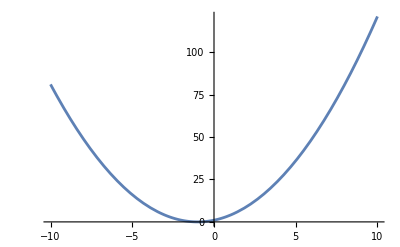

```mathematica
Plot[x^2+2x+1,{x,-10,10}]
```

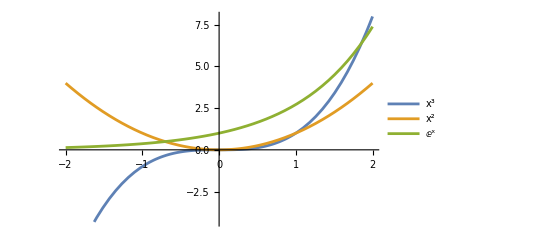

```mathematica
Plot[{x^3,x^2,E^x},{x,-2,2},PlotLegends->"Expressions"]
```

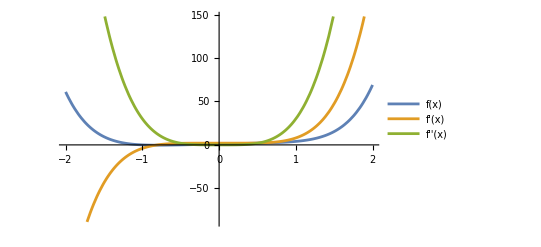

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-2,2},PlotLegends->"Expressions"]
```

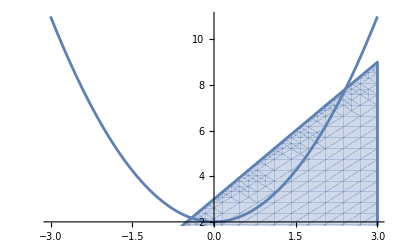

```mathematica
Show[{Plot[x^2+2,{x,-3,3}],RegionPlot[2 x>y-3,{x,-3,3},{y,0,9}]}]
```